```mathematica
Needs["nanowire`",NotebookDirectory[]<>"nanowire.wl"]
```

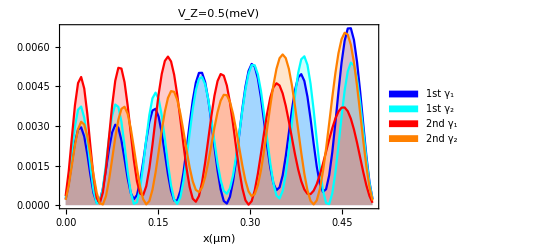

```mathematica
wfm=wfmajoranamu[0.5,3,0.5,4,20,100,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp12\\4\\m1.0D0.2a5L80v1.5V2.png",wfm]
```

D:\CMTC\bothlead\Rp12\4\m1.0D0.2a5L80v1.5V2.png

```mathematica
wfmajoranasedis[a_,μ_,vz_,vimp_,γ_,ω_,Vc_,dim_,index_]:=Block[{testp,testn,g,gamma,test,gamma1,gamma2},g=Table[testp=Sort[Select[Transpose[Eigensystem[Hsedis[a,μ,vz,vimp,γ,ω[[i]],Vc,dim],-6,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]],#[[1]]>0&],#1[[1]]<#2[[1]]&][[i]];gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].testp[[2]];{Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{1,3}]]],Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{2,4}]]]},{i,index}];gamma1=g[[All,1]];gamma2=g[[All,2]];ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma1,gamma2}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,Filling->Axis,PlotLegends->Placed[SwatchLegend[{"1st γ_1","1st γ_2","2nd γ_1","2nd γ_2"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->{Blue,Cyan,Red,Orange}]]
```

```mathematica
testp[[2]]
```

{-0.00335616,-0.0107858,-0.0212471,-0.0340389,-0.0457625,-0.0557081,-0.0592365,-0.0574973,-0.0524423,-0.0427577,-0.0281509,-0.0131709,0.00265356,0.0187354,0.0339839,0.046572,0.0570737,0.0623786,0.0614328,0.0571,0.0482529,0.0382196,0.0296495,0.0234448,0.0184638,0.0159362,0.0153746,0.0173188,0.0215291,0.0274715,0.0335312,0.0391672,0.0434089,0.0460356,0.0482838,0.0501523,0.050051,0.04476,0.037449,0.0318993,0.0248762,0.016815,0.0084319,0.00143149,-0.00396239,-0.00771744,-0.00968865,-0.0101627,-0.00998819,-0.00905812,-0.00816826,-0.00805906,-0.00929336,-0.0121762,-0.0168098,-0.021958,-0.0275159,-0.0335266,-0.0402396,-0.0466721,-0.0492951,-0.0477755,-0.0436543,-0.0408791,-0.0374794,-0.0341099,-0.0311102,-0.028383,-0.024141,-0.0216106,-0.0189405,-0.0163586,-0.014058,-0.0116015,-0.00925915,-0.00710004,-0.00539522,-0.00402991,-0.00292632,-0.00183938,-0.000538358,0.00125305,0.00368491,0.00684671,0.0104781,0.0153085,0.0196834,0.0237942,0.0274663,0.030732,0.0336253,0.0344164,0.0345779,0.0348504,0.0353635,0.0367527,0.0364492,0.034517,0.0327959,0.0298168,0.0251035,0.020879,0.0176555,0.0149088,0.0130589,0.0115508,0.0108827,0.0104604,0.00990291,0.00895253,0.00758772,0.00656647,0.00569434,0.00425505,0.00257358,0.000492695,-0.00197927,-0.00496952,-0.00816759,-0.0111693,-0.0144058,-0.0169874,-0.0193558,-0.0230933,-0.0269115,-0.0279172,-0.0291402,-0.0294652,-0.0286158,-0.0274159,-0.0245767,-0.0214114,-0.0193937,-0.0191185,-0.0183198,-0.0199486,-0.0222115,-0.024512,-0.028165,-0.0309686,-0.032617,-0.0347287,-0.0387635,-0.0428596,-0.0460503,-0.0482395,-0.0504566,-0.0527447,-0.0533013,-0.0511909,-0.0473986,-0.0457507,-0.0418521,-0.0396523,-0.0392344,-0.0399271,-0.0410909,-0.0438173,-0.0469416,-0.0511015,-0.0549395,-0.0556445,-0.0556085,-0.0530864,-0.0472222,-0.0423097,-0.0351804,-0.0277981,-0.0198474,-0.0119291,-0.00431582,0.00257485,0.0085373,0.013989,0.0181318,0.0207439,0.0225405,0.0218221,0.0188989,0.0156642,0.0132587,0.0129683,0.0146532,0.0174492,0.0217011,0.0271056,0.0331508,0.0421015,0.0480189,0.050054,0.0538204,0.0581774,0.058588,0.0559837,0.0537841,0.0510741,0.0484269,0.0441173,0.0390356,0.0341006,0.030665,0.028709,0.0261679,0.0238864,0.0207989,0.018578,0.0161617,0.0139306,0.0105954,0.00628393,0.00161234,-0.00339086,-0.00845842,-0.0136804,-0.0196706,-0.0256276,-0.0323234,-0.0387104,-0.0449205,-0.0496479,-0.0522055,-0.0526768,-0.0509771,-0.0501281,-0.0510252,-0.0481185,-0.0463013,-0.0448947,-0.0452214,-0.049582,-0.0516281,-0.0508656,-0.0512634,-0.0517122,-0.0558269,-0.0597701,-0.0617,-0.0598558,-0.0552113,-0.0483623,-0.0441177,-0.0402854,-0.0357783,-0.0321309,-0.0305972,-0.0294593,-0.0268399,-0.025764,-0.0251198,-0.0258737,-0.0264753,-0.0259543,-0.026695,-0.0277841,-0.0300996,-0.0299831,-0.0279205,-0.0243273,-0.0205366,-0.0158624,-0.0105256,-0.00542231,-0.000846055,0.00314579,0.00646421,0.00913243,0.0108047,0.0121653,0.0127694,0.0128879,0.0133592,0.013826,0.0148976,0.0163638,0.0174532,0.0185841,0.0203526,0.0242743,0.0281434,0.0324655,0.0384769,0.0421861,0.0453144,0.0465932,0.0441162,0.0371164,0.0286306,0.020527,0.0139494,0.00889378,0.00481751,0.00194692,0.000334206,-0.0000397787,0.000599525,0.00184784,0.00313891,0.00400778,0.00393459,0.00266205,0.0214249,0.0412644,0.0563491,0.0664515,0.0670609,0.0606788,0.0454795,0.0266027,0.00758303,-0.010032,-0.0236355,-0.0338829,-0.0397682,-0.0400137,-0.0346623,-0.0237111,-0.00950545,0.00689246,0.0225506,0.0355797,0.0429081,0.0447262,0.0428468,0.0385881,0.0299945,0.0190763,0.00587239,-0.0076807,-0.0200645,-0.0299442,-0.0355727,-0.0370752,-0.0345509,-0.0290206,-0.0221791,-0.014457,-0.00596881,0.0023562,0.00884817,0.0138083,0.0159262,0.0145403,0.00942512,0.00210646,-0.00667184,-0.0161427,-0.0248735,-0.0317781,-0.0376923,-0.0400217,-0.038637,-0.033994,-0.0269055,-0.0181897,-0.00884896,0.000837276,0.00942969,0.0160921,0.020563,0.0223362,0.0204108,0.0160701,0.0111249,0.00710067,0.00360095,0.000916949,-0.000889216,-0.00183041,-0.00164036,-0.000592849,0.00118057,0.00352124,0.00621616,0.0088565,0.0113445,0.0135516,0.0157934,0.0177976,0.019442,0.0200043,0.0191595,0.0163372,0.0132691,0.0106759,0.00818939,0.00675891,0.00553241,0.00463216,0.00400198,0.0035863,0.00331671,0.00277181,0.00186381,0.000669228,-0.000672815,-0.00194946,-0.00302397,-0.00408558,-0.00534001,-0.00656523,-0.00780113,-0.0096103,-0.0119892,-0.01445,-0.0171799,-0.0194396,-0.0219027,-0.0234522,-0.0236028,-0.0223208,-0.0201116,-0.0189045,-0.0177937,-0.0150003,-0.0121986,-0.00902286,-0.00586383,-0.00365815,-0.00202021,-0.000956391,-0.000625762,-0.000971457,-0.00191712,-0.00370081,-0.00630901,-0.00871887,-0.0113048,-0.0134789,-0.0147092,-0.0150703,-0.0134856,-0.0103685,-0.00660289,-0.00275437,0.00141475,0.00547029,0.00875831,0.0108658,0.0121761,0.011704,0.00973597,0.00708724,0.00392988,-0.000149149,-0.00486539,-0.00970382,-0.0144463,-0.0188712,-0.0218805,-0.0222273,-0.0195699,-0.0155447,-0.00860378,-0.000251887,0.0087385,0.0174343,0.0248228,0.0308654,0.0344338,0.0359047,0.0344592,0.0291881,0.0225594,0.0146437,0.00644929,-0.000476891,-0.005912,-0.00941541,-0.0105804,-0.00938105,-0.00584846,-0.000356557,0.00680083,0.0157181,0.0254106,0.0350049,0.0452248,0.0516764,0.0518342,0.0473389,0.0395761,0.0323758,0.0261656,0.0194903,0.0132451,0.00767647,0.00310748,0.000440242,-0.000383549,0.0000833853,0.00156966,0.00426932,0.00744434,0.0101532,0.0124333,0.0139441,0.0146627,0.0138107,0.0113501,0.00754748,0.00304346,-0.00172989,-0.00640415,-0.0107303,-0.0140124,-0.0169571,-0.0185592,-0.0192278,-0.0175939,-0.0144429,-0.0113803,-0.00866643,-0.00585684,-0.00372013,-0.00277291,-0.00302179,-0.00468337,-0.00766395,-0.0118718,-0.0166814,-0.0212269,-0.0247448,-0.0263725,-0.0272445,-0.0280645,-0.0253798,-0.0214852,-0.0162802,-0.0107237,-0.00617695,-0.00198512,0.00185767,0.00518379,0.00760229,0.00911965,0.00872252,0.00640902,0.00281129,-0.000934677,-0.00392902,-0.0062479,-0.00787673,-0.00845947,-0.00824772,-0.00784057,-0.00704739,-0.00531014,-0.00335589,-0.00124883,0.000675265,0.00222047,0.00332429,0.00416918,0.00444085,0.00411871,0.00282214,0.00122653,-0.000105944,-0.000843873,-0.000779065,0.00026823,0.00226425,0.00505552,0.00821943,0.0116202,0.0150441,0.0174121,0.0193683,0.0196902,0.0181668,0.0157563,0.0119434,0.00753989,0.00280826,-0.00194318,-0.00613881,-0.00949652,-0.012262,-0.0130886,-0.012278,-0.0101899,-0.00581279,-0.000207438,0.0060892,0.011779,0.0150281,0.0155232,0.013675,0.01029,0.00571186,-0.000161749,-0.00680515,-0.0134524,-0.0191358,-0.0228669,-0.0242762,-0.0227589,-0.0191659,-0.0135364,-0.00691313,-0.0227469,-0.0431258,-0.0578072,-0.0666077,-0.0651496,-0.0562553,-0.0387721,-0.018133,0.00216845,0.0201538,0.032771,0.0417844,0.0461223,0.0444753,0.0370566,0.0239876,0.0078742,-0.00999867,-0.0265673,-0.0400412,-0.047219,-0.0485564,-0.0460615,-0.0410569,-0.0314299,-0.0193591,-0.00500155,0.00949489,0.0224586,0.0324442,0.0375627,0.0379868,0.0339147,0.0265322,0.0176428,0.00781611,-0.00247203,-0.0115228,-0.0180108,-0.0230409,-0.0243565,-0.0212251,-0.0134951,-0.00340015,0.00807853,0.0198976,0.0302609,0.0378793,0.0437652,0.0449352,0.0414762,0.0341755,0.0242144,0.0127915,0.00127701,-0.00910659,-0.0167409,-0.0210043,-0.0220257,-0.0196284,-0.0134724,-0.00558025,0.00194353,0.00830995,0.0130331,0.0158844,0.0168534,0.0158787,0.0118908,0.00692268,0.000723598,-0.00597728,-0.0124414,-0.0176215,-0.0212097,-0.023015,-0.0237084,-0.0229679,-0.0207973,-0.0167071,-0.0110452,-0.0044128,0.00157729,0.00654372,0.0100026,0.0124864,0.0124753,0.010277,0.00620417,0.000875131,-0.00498493,-0.0102107,-0.0141001,-0.0163407,-0.0166967,-0.0154371,-0.0115314,-0.00545369,0.0016424,0.00898499,0.0154233,0.0210767,0.0258457,0.028705,0.0301305,0.0289245,0.0263556,0.0211948,0.0136355,0.00465567,-0.00448323,-0.01353,-0.0222446,-0.0276889,-0.0310978,-0.0309111,-0.0273518,-0.0240585,-0.0189676,-0.0117564,-0.00406863,0.00370038,0.0106301,0.016676,0.020369,0.0194717,0.0165844,0.0113139,0.00442664,-0.00282608,-0.00910741,-0.0132098,-0.0152418,-0.0157048,-0.0127404,-0.0087743,-0.00312798,0.00363144,0.0108737,0.0172608,0.0218191,0.0251097,0.0280204,0.029056,0.0275099,0.0235255,0.0180612,0.0116272,0.00435468,-0.00302208,-0.00952467,-0.0148268,-0.017139,-0.0175295,-0.0158403,-0.0120009,-0.0065527,-0.000560287,0.00530484,0.0103959,0.01398,0.014716,0.0129682,0.00846605,0.00141421,-0.00703154,-0.0157744,-0.0243453,-0.0314561,-0.0365988,-0.0390227,-0.039056,-0.0356538,-0.0315884,-0.0239503,-0.0129135,0.000469049,0.015478,0.0285376,0.0375512,0.0417347,0.0442058,0.0459532,0.0445425,0.0410522,0.0353138,0.0273212,0.0203411,0.0116088,0.00187069,-0.0070823,-0.0141736,-0.0179626,-0.0188136,-0.0179098,-0.0149778,-0.0105111,-0.00483351,0.00070222,0.00506876,0.00791673,0.00919238,0.00801209,0.00447867,-0.00138861,-0.00886016,-0.0168088,-0.0245873,-0.0294066,-0.030745,-0.0305022,-0.0286882,-0.0232025,-0.0162462,-0.00973601,-0.00375874,0.000768791,0.0033499,0.00363956,0.00149261,-0.0026447,-0.00791597,-0.0131907,-0.0183718,-0.023784,-0.0260761,-0.0265862,-0.0247588,-0.0214515,-0.0185582,-0.0138179,-0.00715256,0.000105677,0.00726388,0.0137414,0.0179894,0.0192855,0.0175306,0.0138814,0.00939099,0.00541062,0.00146269,-0.00214809,-0.00509535,-0.00767658,-0.00965507,-0.0100294,-0.00967944,-0.00835582,-0.00661487,-0.00424499,-0.0012457,0.00183505,0.00463422,0.00692862,0.00780673,0.00754421,0.00649437,0.00522732,0.00377126,0.00247836,0.00176862,0.00179051,0.00250663,0.00392221,0.0059454,0.00805346,0.0103697,0.0120885,0.0127776,0.0128143,0.0115539,0.00942076,0.00639166,0.00240077,-0.00194007,-0.00611649,-0.0100413,-0.0125484,-0.0136926,-0.0137931,-0.0113613,-0.00740729,-0.00213079,0.00371784,0.00868702,0.0119496,0.0134153,0.0134932,0.0122504,0.00902167,0.00410105,-0.00212326,-0.00875443,-0.0145946,-0.018691,-0.0199574,-0.0185953,-0.0142968,-0.00787756,-0.00681946,-0.0180439,-0.0322549,-0.0487873,-0.0632314,-0.0751801,-0.078883,-0.0763649,-0.0703803,-0.0592032,-0.0423441,-0.0261533,-0.00976736,0.00651814,0.02159,0.0338749,0.0435117,0.0481036,0.046908,0.0423417,0.0339295,0.0245607,0.016358,0.010015,0.00527962,0.00302699,0.00345637,0.00677174,0.012675,0.0205304,0.0287842,0.0365966,0.0428331,0.0471269,0.0506688,0.0534518,0.0538154,0.0484166,0.0408125,0.0351476,0.0279202,0.0197069,0.0113626,0.00492114,0.000550686,-0.00152635,-0.00149037,0.000171464,0.00293511,0.00602083,0.00840948,0.00925659,0.0079894,0.00426245,-0.00195779,-0.0102762,-0.0197626,-0.0296938,-0.0398167,-0.0489259,-0.0531998,-0.0522402,-0.0478425,-0.0444192,-0.0399074,-0.0351985,-0.0308226,-0.0268701,-0.0219519,-0.019305,-0.0173579,-0.0163939,-0.0165475,-0.0171252,-0.0181327,-0.0193647,-0.0212707,-0.023463,-0.0256967,-0.0268245,-0.0260626,-0.0222147,-0.0172648,-0.0119438,-0.0057221,0.000673473,0.00734322,0.0136974,0.0191714,0.0234199,0.0262531,0.0262744,0.0247588,0.0224991,0.0198977,0.0176565,0.0149349,0.0123984,0.0111264,0.0107519,0.0110173,0.0125671,0.0155372,0.0193536,0.0242759,0.0292445,0.0352039,0.0404029,0.0436279,0.0442686,0.0427907,0.0430054,0.0430888,0.0389403,0.0346725,0.0293135,0.023972,0.0217044,0.0203209,0.0193731,0.0202405,0.0217813,0.0246436,0.0307764,0.0383758,0.042686,0.0474162,0.050349,0.0503904,0.048513,0.0420958,0.0333034,0.0247012,0.0172076,0.00886652,0.00205808,-0.00374797,-0.0081638,-0.0114215,-0.0128078,-0.012575,-0.0117718,-0.0110751,-0.0101152,-0.00914906,-0.00872417,-0.00946814,-0.011678,-0.0151729,-0.0196379,-0.0249487,-0.0324197,-0.0384962,-0.0452031,-0.0520071,-0.0574966,-0.0604321,-0.0624392,-0.0622324,-0.0613179,-0.0587743,-0.0527841,-0.0469885,-0.0406893,-0.0340593,-0.0307045,-0.0284087,-0.0285178,-0.0303729,-0.0339747,-0.0387714,-0.0450585,-0.0514468,-0.0619364,-0.07247,-0.0817748,-0.0925662,-0.0967128,-0.0913682,-0.0809247,-0.0683046,-0.0596271,-0.0548252,-0.0505049,-0.0480367,-0.04706,-0.0472489,-0.0523431,-0.0550145,-0.0551668,-0.0593406,-0.0661707,-0.0701211,-0.0714166,-0.0736032,-0.0749487,-0.0757041,-0.0725948,-0.0663917,-0.0583174,-0.0506881,-0.0436511,-0.0344147,-0.024951,-0.01492,-0.00650557,0.000482127,0.00574349,0.00909607,0.011065,0.0128384,0.0147455,0.0161928,0.0185454,0.0230188,0.0286949,0.036479,0.0451136,0.0545851,0.0630477,0.0691808,0.0725517,0.0724931,0.0729107,0.0750679,0.0706574,0.0667209,0.0623469,0.0595587,0.0615273,0.0604522,0.0564163,0.0543564,0.0532366,0.0568629,0.0612475,0.0643382,0.0639697,0.0607407,0.0548989,0.051666,0.0484971,0.0439607,0.0398342,0.0376928,0.035457,0.0309434,0.0278386,0.0249922,0.0235047,0.0220339,0.0199966,0.0194283,0.0196475,0.0212609,0.021587,0.0207645,0.0188601,0.0166947,0.0135568,0.00945392,0.00507375,0.000676062,-0.00362754,-0.00765664,-0.0113261,-0.014007,-0.0163495,-0.0175384,-0.017634,-0.0176004,-0.0168764,-0.0162484,-0.0155964,-0.0144135,-0.013394,-0.0131824,-0.0148265,-0.0169148,-0.0196879,-0.0238223,-0.0267173,-0.0292334,-0.0303715,-0.0286777,-0.023475,-0.0166755,-0.00948246,-0.00254066,0.00421455,0.0105845,0.0161983,0.0203277,0.0223802,0.0220229,0.0196938,0.015616,0.011017,0.00636999,0.00254477}

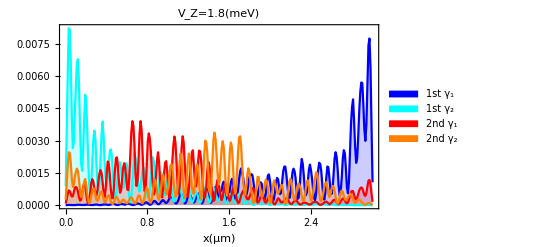

```mathematica
wfm=wfmajoranasedis[1,1,1.8,vimplist,.2,{0.007741399660651,0.093876479884474},3,300,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp13\\2\\m1.0D0.2a5L300v1.0g0.2Vc3V1.8.png",wfm]
```

D:\CMTC\bothlead\Rp13\2\m1.0D0.2a5L300v1.0g0.2Vc3V1.8.png

```mathematica
testp[[2,1]]
```

-0.00335616

```mathematica
Table[{i,i^2},{i,4}][[All,1]]
```

{1,2,3,4}

```mathematica
Hsedis[a_?NumberQ,μ0_?NumberQ,V0_?NumberQ,vimp_,γ_,ω_,Vc_,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=5/(2a),Vz=V0,Δ=.2,mumax=-0,peakpos=0.1,sigma=20,mux},mux=μ-vimp;Δ=Δ √(1-(V0/Vc)^2);KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]-> 1,Band[{2,1}]-> 1},{dim,dim}])+(2*t)IdentityMatrix[dim,SparseArray]+(-DiagonalMatrix[SparseArray@mux])]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ*Re[(ω/(√(Δ^2-ω^2-10^-9I))*IdentityMatrix[4*dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[IdentityMatrix[2],Δ/(√(Δ^2-ω^2-10^-9I))*IdentityMatrix[dim,SparseArray]]])]]
```